```mathematica
(*Измерение спектра источника*)
A={145862.6,350.0,771.2,179.6,26.2,33.0,70.8,109.8,151.0,178.6,196.8,183.8,143.0,83.6,47.8,23.2,10.8,5.8,6.0,4.6}
```

{145863.,350.,771.2,179.6,26.2,33.,70.8,109.8,151.,178.6,196.8,183.8,143.,83.6,47.8,23.2,10.8,5.8,6.,4.6}

```mathematica
A*0.08
```

{11669.,28.,61.696,14.368,2.096,2.64,5.664,8.784,12.08,14.288,15.744,14.704,11.44,6.688,3.824,1.856,0.864,0.464,0.48,0.368}

```mathematica
X=Array[#*0.5&,20,0]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5}

```mathematica
Spectre=Transpose[{X}].({{1, 0}})+Transpose[{A}].({{0, 1}})
```

{{0.,145863.},{0.5,350.},{1.,771.2},{1.5,179.6},{2.,26.2},{2.5,33.},{3.,70.8},{3.5,109.8},{4.,151.},{4.5,178.6},{5.,196.8},{5.5,183.8},{6.,143.},{6.5,83.6},{7.,47.8},{7.5,23.2},{8.,10.8},{8.5,5.8},{9.,6.},{9.5,4.6}}

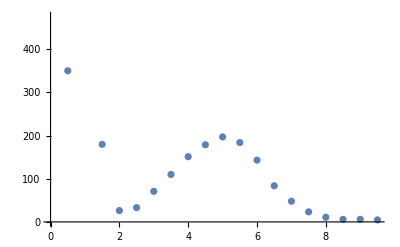

```mathematica
ListPlot[Spectre]
```

```mathematica
data=Spectre[[5;;20]]
```

{{2.,26.2},{2.5,33.},{3.,70.8},{3.5,109.8},{4.,151.},{4.5,178.6},{5.,196.8},{5.5,183.8},{6.,143.},{6.5,83.6},{7.,47.8},{7.5,23.2},{8.,10.8},{8.5,5.8},{9.,6.},{9.5,4.6}}

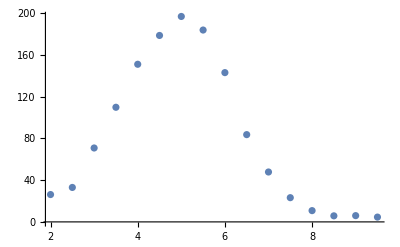

```mathematica
ListPlot[data]
```

```mathematica
errors=(A*0.08)[[5;;20]];
ampl Evaluate[PDF[NormalDistribution[x0,sigma],x]]
nlm=NonlinearModelFit[data,ampl Evaluate[PDF[NormalDistribution[x0,sigma],x]],{ampl,x0,sigma},{x}, Weights->1/errors];
GaussianFit=nlm["BestFit"]
nlm["ParameterTable"]
```

(ampl ⅇ^(-(x-x0)^2/(2 sigma^2)))/(√(2 π) sigma)

192.906 ⅇ^(-0.289343 (-4.87281+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
ampl | 635.644 | 18.8358 | 33.7465 | 4.79036×10^-14
x0 | 4.87281 | 0.0404714 | 120.401 | 3.36272×10^-21
sigma | 1.31455 | 0.0325766 | 40.3527 | 4.7859×10^-15

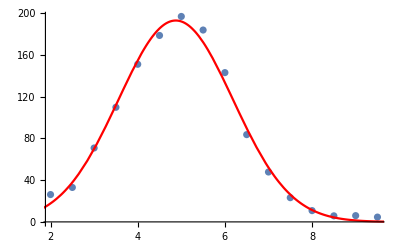

```mathematica
Show[ListPlot[data],Plot[GaussianFit,{x,0,10},PlotStyle->Red]]
```

```mathematica
Reduce[D[GaussianFit,x]==0]
```

x==4.87281

```mathematica
Coef1=ampl/(√(2π)sigma);
sigmaX=Sqrt[D[Coef1,ampl]^2*18.84^2+D[Coef1,sigma]^2*0.033^2]/.{ampl-> 635.64,sigma->1.314}
```

7.49724

```mathematica
(*Измерение резонансного поглощения*)
```

```mathematica
Sn100=({{0.0, 913.2}, {-1.44, 871.7}, {-1.52, 852.1}, {-1.48, 858.4}, {-1.37, 852.4}, {-1.21, 834.4}, {-4.44, 856.6}, {-3.71, 845.9}, {-3.08, 857.9}, {-2.48, 847.0}, {-2.12, 841.9}, {-1.57, 858.0}, {-1.55, 841.3}, {-1.06, 857.6}, {-2.62, 869.2}, {-1.57, 858.0}, {-1.55, 841.3}, {-1.06, 857.6}, {-2.62, 869.2}, {-2.83, 869.1}, {-2.99, 852.9}, {-2.16, 850.5}, {-1.85, 856.1}, {-2.34, 854.7}, {-2.11, 858.0}, {-1.93, 838.0}, {-2.25, 845.6}, {1.52, 853.3}, {1.61, 850.1}, {1.59, 843.1}, {1.51, 853.6}, {1.35, 842.6}, {4.71, 848.4}, {3.92, 846.7}, {3.27, 840.0}, {2.64, 750.8}, {1.67, 838.1}, {1.64, 837.1}, {1.16, 841.4}, {2.79, 764.0}, {3.00, 793.3}, {3.16, 812.6}, {3.49, 828.7}, {3.12, 815.8}, {2.82, 778.5}, {2.32, 762.0}, {1.99, 812.8}, {2.48, 755.3}, {2.22, 792.8}, {2.04, 799.9}, {2.41, 764.4}});
Sn200=({{-2.67, 384.7}, {-3.09, 382.7}, {-3.50, 385.8}, {-3.90, 380.3}, {-4.32, 384.4}, {-2.44, 379.3}, {-1.65, 381.8}, {-1.99, 385.8}, {-2.70, 382.2}, {-2.93, 368.9}, {-3.04, 371.2}, {-2.67, 379.3}, {-2.43, 379.6}, {-2.17, 380.6}, {-1.94, 372.2}, {-1.72, 373.0}, {-1.45, 390.0}, {-1.14, 384.6}, {-0.70, 375.7}, {-1.65, 396.0}, {-1.90, 374.7}, {2.83, 314.1}, {3.26, 347.2}, {3.73, 372.8}, {4.14, 372.4}, {4.55, 374.1}, {2.61, 311.5}, {1.78, 366.7}, {2.12, 329.0}, {2.84, 324.7}, {3.12, 342.6}, {3.24, 365.9}, {2.82, 327.2}, {2.56, 317.5}, {2.31, 313.9}, {2.07, 338.1}, {1.85, 346.9}, {1.54, 360.9}, {1.20, 379.5}, {0.77, 371.8}, {1.77, 358.3}, {2.04, 337.1}});
SnO2=({{-0.72, 610.6}, {-0.87, 606.0}, {-1.14, 654.2}, {-1.43, 686.3}, {-1.29, 673.3}, {-1.06, 652.9}, {-2.80, 743.4}, {-3.42, 757.9}, {-4.12, 750.2}, {-4.50, 751.7}, {-2.51, 739.3}, {-2.24, 745.6}, {-1.65, 704.4}, {-1.08, 661.9}, {-0.33, 550.3}, {-0.21, 544.0}, {-0.48, 565.0}, {-0.73, 603.3}, {0.76, 619.4}, {0.93, 628.5}, {1.21, 667.1}, {1.53, 692.2}, {1.38, 682.8}, {1.23, 669.3}, {2.98, 758.8}, {3.59, 758.1}, {4.37, 769.7}, {4.77, 772.0}, {2.64, 744.0}, {2.39, 750.5}, {1.76, 728.2}, {1.16, 649.2}, {0.39, 556.9}, {0.25, 546.3}, {0.53, 591.6}, {0.75, 611.1}});
```

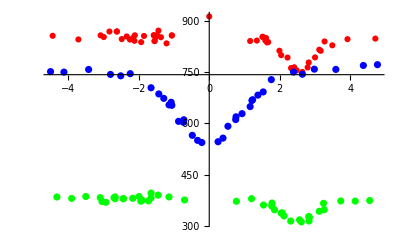

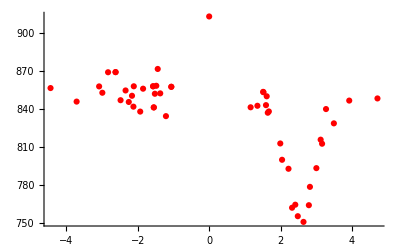

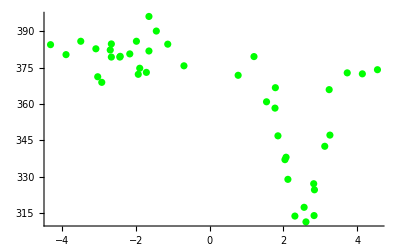

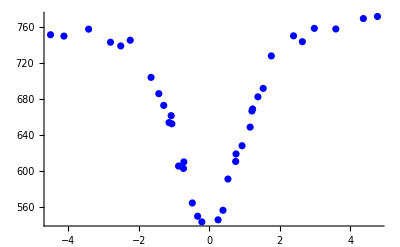

```mathematica
Show[
ListPlot[Sn100, PlotStyle->Red],
ListPlot[Sn200,PlotStyle->Green],
ListPlot[SnO2,PlotStyle->Blue], PlotRange->All
]
ListPlot[Sn100, PlotStyle->Red]
ListPlot[Sn200,PlotStyle->Green]
ListPlot[SnO2,PlotStyle->Blue]
```